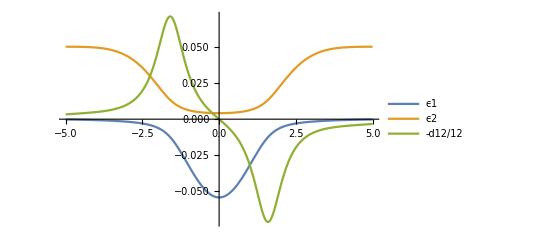

```mathematica
(* define electronic Hamiltonian *)
A0 = 0.10;
B0 = 0.28;
C0 = 0.015;
D0 = 0.06;
E0 = 0.05;
H = ( {
    {0, C0 E^(-D0 x^2)},
    {C0 E^(-D0 x^2), -A0 E^(-B0 x^2) + E0}
   } );

(* solve electronic Hamiltonian *)
{{ϵ1, ϵ2}, {v1,v2}} = Eigensystem[H];
v1 /= Sqrt[v1.v1];
v2 /= Sqrt[v2.v2];

(* find nonadiabatic coupling of adiabatic states *)
d12 = v1.D[v2, x];

(* check surfaces *)
Plot[{ϵ1, ϵ2, -d12/12.}, {x, -5, 5}, 
 PlotLegends -> {"ϵ1", "ϵ2", "-d12/12"}]
```

```mathematica
linspace[start_,end_,n_:100]:=Table[N[x],{x,start,end,(end-start)/(n-1)}];
xgrid = linspace[-10,10,100];
Export[NotebookDirectory[]<>"Tully-model2-e1.dat",Table[{x,ϵ1},{x,xgrid}]]
Export[NotebookDirectory[]<>"Tully-model2-e2.dat",Table[{x,ϵ2},{x,xgrid}]]
Export[NotebookDirectory[]<>"Tully-model2-d12.dat",Table[{x,d12},{x,xgrid}]]
```

/home/yyang173/Desktop/fewest_switch/Tully-model2-e1.dat

/home/yyang173/Desktop/fewest_switch/Tully-model2-e2.dat

/home/yyang173/Desktop/fewest_switch/Tully-model2-d12.dat